```mathematica
(** This is code modified specifically for the 2d case **)
(** Set the directory that you want your plots to go to here **)
SetDirectory["/users/maxzweig/fuelthrust"];

Off[Solve::svars];
Off[FindRoot::lstol];
Off[InterpolatingFunction::dmval];

vectoangle[k_] :=ArcTan[k[[1]],k[[2]]];

(** gets the axes for the energy limited reachable set associated with a given terminal time and thrust **)

getAxes[terminaltime_, quadform_, thrustmax_] := Module[{testbounds, teststats},
energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];
ax1 = vecs[[1]][[1;;2]] * ((terminaltime thrustmax^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((terminaltime thrustmax^2* vals[[2]]) // Sqrt);
{ax1,ax2}]

(** gets the minimum and maximum ratios between an energy limited set and an arbitrary reachable set given as set of points **)
reachablestatsoperator[points_,axis1_,axis2_] := Module[{rats, vecs}, 
Print[Dimensions[points]];
Print[points[[1]]];
ellipseVecFromUnitVec[uv_,ax1_, ax2_]:=1/Sqrt[(Normalize[ax1].uv)^2/Norm[ax1]^2+(Normalize[ax2].uv)^2/Norm[ax2]^2]*uv;
ratio[pos_]:= Norm[ellipseVecFromUnitVec[Normalize[pos[[1;;2]]],axis1, axis2] ]/ Norm[pos[[1;;2]]];
maxminrat[ v1s_] := {(ratio/@v1s)// Max, (ratio/@v1s)// Min};
toq2q1[vec_] := If[(vec[[1]] < 0 && vec[[2]] < 0) || (vec[[1]] >0 && vec[[2]] < 0), -vec, vec];
maxminvec[ v1s_] := {v1s[[ Position[(ratio/@v1s), (ratio/@v1s) // Max    ][[1,1]]]] // toq2q1 , v1s[[ Position[(ratio/@v1s), (ratio/@v1s) // Min   ][[1,1]]]] // toq2q1};
rats = maxminrat[ points];
vecs = maxminvec[ points];
{rats , {vecs[[1, 1;;2]], vecs[[2, 1;;2]]}}
] ;

(* computes minimum and maximum ratios between the thrust limited and thrust/fuel limited reachable sets, given as a set of points that are indexed by angle in their arrays.
Assuming given points are angle aligned. *)
thrustfuelstats[thrustpoints_, fuelpoints_] := Module[{rats, vecs},

ListRatios[list1_, list2_] := MapThread[#1/#2&,{list1,list2}];
ratios = ListRatios[Map[Norm, thrustpoints], Map[Norm, fuelpoints]];
maxratio = ratios // Max;
minratio = ratios // Min;

toq2q1[vec_] := If[(vec[[1]] < 0 && vec[[2]] < 0) || (vec[[1]] >0 && vec[[2]] < 0), -vec, vec];

maxpos = Position[ratios, maxratio][[1,1]];
minpos = Position[ratios, minratio][[1,1]];

maxpos = fuelpoints[[maxpos]] // toq2q1;
minpos = fuelpoints[[minpos]] // toq2q1;

{maxratio, minratio, maxpos, minpos}
];
energyform[tff_, na_] := Module[{c, r, sig, gamma, nmat},
c[n_] = {
{0, -2* n, 0, 1, 0, 0},
{2 * n, 0, 0, 0, 1, 0},
{0, 0, 0, 0,0 , 1},
{-1, 0, 0, 0, 0, 0},
{0, -1, 0, 0,0,0 }, 
{0, 0, -1, 0, 0, 0 }
}; (*Good*)
c[n] // MatrixForm;
r[t_, h_] = {{72 t Cos[h t]+(154 h t+48 h^3 t^3-384 Sin[h t]-27 Sin[2 h t])/(4 h),-3 h t^2+(6-6 Cos[h t])/h,0,(8+12 h^2 t^2-8 Cos[h t]-24 h t Sin[h t]+9 Sin[h t]^2)/(2 h^2),(23 h t+6 h^3 t^3+42 h t Cos[h t]-56 Sin[h t]-9/2 Sin[2 h t])/h^2,0},{-3 h t^2+(6-6 Cos[h t])/h,t,0,(2 (-h t+Sin[h t]))/h^2,-(3 t^2)/2+(4-4 Cos[h t])/h^2,0},{0,0,(2 h t+Sin[2 h t])/(4 h),0,0,Sin[h t]^2/(2 h^2)},{(8+12 h^2 t^2-8 Cos[h t]-24 h t Sin[h t]+9 Sin[h t]^2)/(2 h^2),(2 (-h t+Sin[h t]))/h^2,0,(26 h t-32 Sin[h t]+3 Sin[2 h t])/(4 h^3),(3 (-h t+Sin[h t])^2)/h^3,0},{(23 h t+6 h^3 t^3+42 h t Cos[h t]-56 Sin[h t]-9/2 Sin[2 h t])/h^2,-(3 t^2)/2+(4-4 Cos[h t])/h^2,0,(3 (-h t+Sin[h t])^2)/h^3,(14 h t+3 h^3 t^3+24 h t Cos[h t]-32 Sin[h t]-3 Sin[2 h t])/h^3,0},{0,0,Sin[h t]^2/(2 h^2),0,0,-(-2 h t+Sin[2 h t])/(4 h^3)}};(*Good*)
r[t, n] // MatrixForm;
sig[t_, n_] = {{4-3 Cos[n t],0,0,Sin[n t]/n,(2-2 Cos[n t])/n,0},{6 (-n t+Sin[n t]),1,0,(2 (-1+Cos[n t]))/n,-3 t+(4 Sin[n t])/n,0},{0,0,Cos[n t],0,0,Sin[n t]/n},{3 n Sin[n t],0,0,Cos[n t],2 Sin[n t],0},{6 n (-1+Cos[n t]),0,0,-2 Sin[n t],-3+4 Cos[n t],0},{0,0,-n Sin[n t],0,0,Cos[n t]}}; (* Good *)
gamma[t_, t0_, n_] = sig[t, n]. (sig[t0, n] // Inverse);
nmat[t0_, tf_, n_] = (Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2] // Transpose). (c[n] // Transpose). (r[tf, n] // Inverse).c[n].Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2];
nmat[0, tff, na]
];
getFinalEnergyPos[tt_, tmax_, nt_, delta_, rho_] := Module[{},

udd = IdentityMatrix[6] - Outer[Times, Join[{delta[[2]], -delta[[1]]}, {0,0,0,0}], Join[{delta[[2]], -delta[[1]]}, {0,0,0,0}]];
basis = Orthogonalize[udd];
projmat = Join[{basis[[1]]}, basis[[3;;]]] // Transpose;
projmatT = projmat // Transpose;
selectionMat = {{1,0,0,0,0,0}, {0,1,0,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}};
eformxf = energyform[tt, nt][[7;;12, 7;;12]];
ydir = Eigenvectors[{projmatT.selectionMat.projmat, projmatT.eformxf.projmat}][[1]];

xdir = projmat.ydir;
tmag = (tt rho tmax^2 / (xdir.eformxf.xdir)) // Sqrt;
xdir = If[xdir[[1]] delta[[1]] < 0, -xdir, xdir];

Print["energy computation executed"];
xdir tmag
];
propStateCostatev2[ics_, isp_, tf_, tmax_, A_] := Module[{vars, dyn},
mag[lxv_, lyv_, lzv_] :=(lxv ^ 2+ lyv ^2 + lzv ^2) // Sqrt;
switchingfunc [lxv_, lyv_, lzv_, lmag_, mas_, c_] := mag[lxv, lyv, lzv] - lmag mas /c; 
vars={x,y,z,vx,vy,vz,m,lxr,lyr,lzr,lxv,lyv,lzv,lm};
eqnsOpt = Join[(- A // Transpose).{lxr, lyr, lzr, lxv, lyv, lzv}, {(*-*)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2)tmax mag[lxv, lyv, lzv]  / (m ^2)}];
eqnsStateOpt={  2 vy n + 3n^2 x,    -2 n vx, - n^2 z  } + (1/m)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2) tmax (*(-)*){lxv, lyv, lzv} / mag[lxv, lyv, lzv];
dyn=Join[Join[{vx,vy,vz},Join[eqnsStateOpt, {- ( 1/2 +Sign[switchingfunc[lxv, lyv, lzv , lm, m, isp]] / 2)tmax/isp}]],eqnsOpt];
soln =  NDSolveValue[
Join[Thread[(#'[t]&/@vars[[1;;14]])==(dyn/.Thread[vars->(#[t]&/@vars)])],
Thread[(#[0]&/@vars)==ics]],
vars,  {t, tf, tf}, Method -> "BDF"
];
#[tf]&/@soln
]

propStateCostateRecoder[ics_, isp_, tf_, tmax_, A_]:= Module[{vars, dyn},
mag[lxv_, lyv_, lzv_] :=(lxv ^ 2+ lyv ^2 + lzv ^2) // Sqrt;
switchingfunc [lxv_, lyv_, lzv_, lmag_, mas_, c_] := mag[lxv, lyv, lzv] - lmag mas /c; 
vars={x,y,z,vx,vy,vz,m,lxr,lyr,lzr,lxv,lyv,lzv,lm};
eqnsOpt = Join[(- A // Transpose).{lxr, lyr, lzr, lxv, lyv, lzv}, {(*-*)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2)tmax mag[lxv, lyv, lzv]  / (m ^2)}];
eqnsStateOpt={  2 vy n + 3n^2 x,    -2 n vx, - n^2 z  } + (1/m)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2) tmax (*(-)*){lxv, lyv, lzv} / mag[lxv, lyv, lzv];
dyn=Join[Join[{vx,vy,vz},Join[eqnsStateOpt, {- ( 1/2 +Sign[switchingfunc[lxv, lyv, lzv , lm, m, isp]] / 2)tmax/isp}]],eqnsOpt];
switches =  Reap[NDSolveValue[
Join[Thread[(#'[t]&/@vars[[1;;14]])==(dyn/.Thread[vars->(#[t]&/@vars)])],
Thread[(#[0]&/@vars)==ics]],
vars,  {t, 0, tf}, Method -> {"EventLocator", "Event" -> switchingfunc[lxv[t], lyv[t], lzv[t] , lm[t], m[t], isp], "EventAction" :> Sow[t]}
]];
switches
]

findInitialCostates[icRel_, fcRel_, n_, A_, td_, mmax_, m0_, tmax_] := Module[{vars, dyn},
eqnsStateOpt={  2 vy n + 3n^2 x,    -2 n vx, - n^2 z  } - {lxv, lyv, lzv};
eqnsOpt = (- A // Transpose).{lxr, lyr, lzr, lxv, lyv, lzv};
getInitCostates[varMat_,icsRel_,fcsRel_]:=LinearSolve[varMat[[1;;6,7;;12]],fcsRel-varMat[[1;;6,1;;6]].icsRel];
topLeftMatrix=A;
topRightMatrix=ConstantArray[0,{3,6}];
middleLeftMatrix=ConstantArray[0,{3,3}];
middleRightMatrix=-IdentityMatrix[3];
     bottomRightMatrix=-A // Transpose;
bottomLeftMatrix=ConstantArray[0,{6,6}];
fullmatrix = Join[Join[A, Join[ topRightMatrix, Join[middleLeftMatrix, middleRightMatrix, 2]], 2], Join[bottomLeftMatrix, bottomRightMatrix, 2 ] ];
stm[tf_] := MatrixExp[fullmatrix tf];
initCo = getInitCostates[stm[td], icRel, fcRel];
lambdastm[ta_] = MatrixExp[(-A // Transpose) ta];
lma = isp ((lambdastm[mmax isp / tmax].initCo)[[4;;6]]   // Norm)/(m0 - mmax) - NIntegrate[  tmax(((lambdastm[t].initCo)[[4;;6]]) // Norm) / ((m0 - tmax t / isp) ^2), {t, 0, mmax isp / tmax}];
initCoM = Join[initCo, {lma}];
initCoM
]
rootfind[init_, mm_, direction_, A_, m0_, isp_, timeLength_, tm_] := Module[{},
s = MatrixExp[-(A //Transpose) timeLength];
ly = init[[2]];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
cons[dey_, lf_, xf_, mmax_] := Module[{},
udd = (2 // IdentityMatrix) - ({dey} // Transpose).{dey};
c1 ={ (udd.{xf[[1]], xf[[2]]})[[1]] } ;
c2 =  If [timeLength tm / isp<=mmax, {((m0 - xf[[7]]) -timeLength tm / isp)}, {((m0 - xf[[7]]) -mmax)}];
Join[c1, c2] // Flatten
];
falt[joint_]:= Module[{out},
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{joint[[1]] , ly, 0}, ({v4, v5} /. subs ) /. {v1->joint[[1]], v2 ->ly} ], {0, joint[[2]]}]], isp, timeLength, tm, A];
cons[direction, out[[8;;14]], out[[1;;7]] , mm]
];
poss = FindRoot[falt[l], {{l, {init[[1]], init[[3]]} }}, Evaluated->False, PrecisionGoal->20, MaxIterations->10000];
(** if poss does not satisfy the directional and mass constraints within satisfaction, try again with the two other possible values for lambda y, and pick the best **)
{poss[[1, 2, 1]], ly, poss[[1, 2, 2]]}
]
rootfindalt2[init_, mm_, direction_, A_, m0_, isp_, timeLength_, tm_] := Module[{},
s = MatrixExp[-(A //Transpose) timeLength];
lx = init[[1]];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
cons[dey_, lf_, xf_, mmax_] := Module[{},
udd = (2 // IdentityMatrix) - ({dey} // Transpose).{dey};
c1 ={ (udd.{xf[[1]], xf[[2]]})[[1]] } ;
c2 =  If [timeLength tm / isp<=mmax, {(m0 - xf[[7]]) -timeLength tm / isp}, {(m0 - xf[[7]]) -mmax}];
Join[c1, c2] // Flatten
];
falt[joint_]:= Module[{out},
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lx , joint[[1]], 0}, ({v4, v5} /. subs ) /. {v1->lx, v2 ->joint[[1]]} ], {0, joint[[2]]}]], isp, timeLength, tm, A];
cons[direction, out[[8;;14]], out[[1;;7]] , mm]
];
poss = FindRoot[falt[l], {{l, {init[[2]], init[[3]]} }}, Evaluated->False, PrecisionGoal->20];

(** if poss does not satisfy the directional and mass constraints within satisfaction, try again with the two other possible values for lambda y, and pick the best **)
{lx, poss[[1, 2, 1]], poss[[1, 2, 2]]}
]

getReachablePoint[direction_, endTime_, tmax_, n_, m0_, A_, fuelpercent_, isp_] := Module[{},
posf = getFinalEnergyPos[endTime, tmax, n, direction, fuelpercent];
s = MatrixExp[-(A //Transpose) endTime];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
initCostates = findInitialCostates[{0,0,0,0,0,0}, posf, n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax ];
initialGuess2 = Join[{initCostates[[1]], initCostates[[2]]},{initCostates[[7]]}];
Print["root finding"];
lxm2 = rootfind[initialGuess2,  tmax fuelpercent endTime / isp, direction // N, A, m0, isp, endTime, tmax];
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lxm2[[1]], lxm2[[2]], 0}, ({v4, v5} /. subs ) /. {v1->lxm2[[1]], v2 ->lxm2[[2]]}, {0, lxm2[[3]]}]]], isp, endTime, tmax, A];

Print[out[[1;;2]] //  Norm];
Print[out[[1;;2]] // Normalize];
Print[direction // N];
{out, lxm2}
]
solveBVPsNested[initialAngle_, initialGuess_, endTime_, tmax_, n_, m0_, A_, fuelpercent_, isp_, numPoints_] := Module[{},
(** returns the direction the initial costate was computed in, as well as the initial costate 
	initialGuess contains all of the costates. 
  If prevDirectionCostate costate is identically 0, do the energy computation to obtain an initial guess. 
  Homotopy from delta to delta to travese the ring. If / when constraint isn't satisfied, perform the energy computation to obtain a new initial guess and try again.
**)
Print[initialAngle, " ",  initialGuess, " ", endTime, " ", tmax, " ", n, " ", m0, " ", A, " ", fuelpercent, " ", isp, " ", numPoints];
bvpNester[prevAngleCostatePosition_] := Module[{},
prevAngle = prevAngleCostatePosition[[1]];
prevCostate = prevAngleCostatePosition[[2]];
prevPosition = prevAngleCostatePosition[[3]];

nextAngle = prevAngle + 2 * Pi / numPoints;
nextDirection = {Cos[nextAngle], Sin[nextAngle]} // N;

nextCostate = If[prevCostate == {0,0,0}, findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax  (**), n, nextDirection, fuelpercent], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]], prevCostate];

nextGuess = {nextCostate[[1]],nextCostate[[2]], nextCostate[[3]]};
lxm2 = rootfind[nextGuess,  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime, tmax];
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lxm2[[1]], lxm2[[2]], 0}, ({v4, v5} /. subs ) /. {v1->lxm2[[1]], v2 ->lxm2[[2]]}, {0, lxm2[[3]]}]]], isp, endTime, tmax, A];

terminalAngle = If[out[[1]] == 0 && out[[2]] == 0, 10000, ArcTan[out[[1]], out[[2]]]];
terminalMass = m0 - out[[7]];

(** retrying with energy optimal initial guess if necessary**)
 nextGuessReturn = If[Abs[(terminalAngle + Pi) - Mod[nextAngle, 2 Pi]] < 0.00125 && Abs[terminalMass / (tmax fuelpercent endTime / isp) - 1] < 0.01,{lxm2[[1]] , lxm2[[2]] , lxm2[[3]]  }, 
rootfind[findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax , n, nextDirection, fuelpercent], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]],  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime, tmax ]
];

out2 = propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{nextGuessReturn[[1]], nextGuessReturn[[2]], 0}, ({v4, v5} /. subs ) /. {v1->nextGuessReturn[[1]], v2 ->nextGuessReturn[[2]]}, {0, nextGuessReturn[[3]]}]]], isp, endTime, tmax, A];

(** if still failure to perfectly satisfy constraints, retrying with alternate optimization holding x constant and allowing changes in y **)
terminalAngle = If[out2[[1]] == 0 && out2[[2]] == 0, 10000, ArcTan[out2[[1]], out2[[2]]]];
If[ (out2[[1]] == 0  && out2[[2]] ==0)  || Abs[terminalMass / (tmax fuelpercent endTime / isp) - 1] >= 0.001 || Abs[(terminalAngle + Pi) - Mod[nextAngle, 2 Pi]] >= 0.00125,
( res = rootfindalt2[{nextGuessReturn[[1]] , nextGuessReturn[[2]] , nextGuessReturn[[3]] },  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime, tmax];
out3 = propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{res[[1]], res[[2]], 0}, ({v4, v5} /. subs ) /. {v1->res[[1]], v2 ->res[[2]]}, {0, res[[3]]}]]], isp, endTime, tmax, A];
{nextAngle, res , out3[[1;;2]], out3[[7]]}
),{nextAngle, nextGuessReturn, out2[[1;;2]], out2[[7]]}
]
(**{nextAngle, nextGuessReturn, out2[[1;;2]], out2[[7]]}**)
];
NestList[bvpNester, {initialAngle, initialGuess, {0,0,0,0,0,0,0}}, numPoints]
]
solveBVPsNestedAlt[initialGuess_, endTime_, tmax_, n_, m0_, A_, fuelpercent_, isp_, numPoints_, lb_, ub_] := Module[{},
(** returns the direction the initial costate was computed in, as well as the initial costate 
	initialGuess contains all of the costates. 
  If prevDirectionCostate costate is identically 0, do the energy computation to obtain an initial guess. 
  Homotopy from delta to delta to travese the ring. If / when constraint isn't satisfied, perform the energy computation to obtain a new initial guess and try again.
**)
Print[lb, " ", ub, " ",initialGuess, " ", endTime, " ", tmax, " ", n, " ", m0, " ", A, " ", fuelpercent, " ", isp, " ", numPoints];
bvpNester[prevAngleCostatePosition_] := Module[{},
prevAngle = prevAngleCostatePosition[[1]];
prevCostate = prevAngleCostatePosition[[2]];
prevPosition = prevAngleCostatePosition[[3]];

nextAngle = prevAngle + (ub - lb) / numPoints;
nextDirection = {Cos[nextAngle], Sin[nextAngle]} // N;

nextCostate = If[prevCostate == {0,0,0}, findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax , n, nextDirection, fuelpercent], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]], prevCostate];

nextGuess = {nextCostate[[1]],nextCostate[[2]], nextCostate[[3]]};
lxm2 = rootfind[nextGuess,  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime, tmax];
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{lxm2[[1]], lxm2[[2]], 0}, ({v4, v5} /. subs ) /. {v1->lxm2[[1]], v2 ->lxm2[[2]]}, {0, lxm2[[3]]}]]], isp, endTime, tmax, A];

terminalAngle = If[out[[1]] == 0 && out[[2]] == 0, 10000, ArcTan[out[[1]], out[[2]]]];
terminalMass = m0 - out[[7]];


(** retrying with energy optimal initial guess if necessary**)
 nextGuessReturn = If[Abs[(terminalAngle + Pi) - Mod[nextAngle, 2 Pi]] < 0.00125 && Abs[terminalMass / (tmax fuelpercent endTime / isp) - 1] < 0.01,{lxm2[[1]] , lxm2[[2]] , lxm2[[3]]  }, 
rootfind[findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax , n, nextDirection, fuelpercent], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]],  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime, tmax ]
];

out2 = propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{nextGuessReturn[[1]], nextGuessReturn[[2]], 0}, ({v4, v5} /. subs ) /. {v1->nextGuessReturn[[1]], v2 ->nextGuessReturn[[2]]}, {0, nextGuessReturn[[3]]}]]], isp, endTime, tmax, A];

(** if still failure to perfectly satisfy constraints, retrying with alternate optimization holding x constant and allowing changes in y **)
terminalAngle = If[out2[[1]] == 0 && out2[[2]] == 0, 10000, ArcTan[out2[[1]], out2[[2]]]];
If[ (out2[[1]] == 0  && out2[[2]] ==0)  || Abs[terminalMass / (tmax fuelpercent endTime / isp) - 1] >= 0.001 || Abs[(terminalAngle + Pi) - Mod[nextAngle, 2 Pi]] >= 0.00125,
( res = rootfindalt2[{nextGuessReturn[[1]] , nextGuessReturn[[2]] , nextGuessReturn[[3]] },  tmax fuelpercent endTime / isp, nextDirection, A, m0, isp, endTime, tmax];
out3 = propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{res[[1]], res[[2]], 0}, ({v4, v5} /. subs ) /. {v1->res[[1]], v2 ->res[[2]]}, {0, res[[3]]}]]], isp, endTime, tmax, A];
{nextAngle, res , out3[[1;;2]], out3[[7]]}
),{nextAngle, nextGuessReturn, out2[[1;;2]], out2[[7]]}
]
(**{nextAngle, nextGuessReturn, out2[[1;;2]], out2[[7]]}**)
];
NestList[bvpNester, {lb, initialGuess, {0,0,0,0,0,0,0}}, numPoints]
]

energyBVPsNested[initialAngle_, initialGuess_, endTime_, tmax_, n_, m0_, A_, fuelpercent_, isp_, numPoints_] := Module[{},
(** returns the direction the initial costate was computed in, as well as the initial costate 
	initialGuess contains all of the costates. 
  If prevDirectionCostate costate is identically 0, do the energy computation to obtain an initial guess. 
  Homotopy from delta to delta to travese the ring. If / when constraint isn't satisfied, perform the energy computation to obtain a new initial guess and try again.
**)
bvpNester[prevAngleCostatePosition_] := Module[{},
prevAngle = prevAngleCostatePosition[[2]];
prevCostate = prevAngleCostatePosition[[1]];

nextAngle = prevAngle + 2 * Pi / numPoints;
nextDirection = {Cos[nextAngle], Sin[nextAngle]} // N;

(** computing the next energy optimal initial costate **)
nextCostate = findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmax (**), n, nextDirection, fuelpercent], n, A, endTime, tmax fuelpercent endTime / isp, m0, tmax / m0 ][[{1, 2, 7}]];
{{nextCostate[[1]],nextCostate[[2]], nextCostate[[3]]}, nextAngle}
];
NestList[bvpNester, {initialGuess, initialAngle}, numPoints]
]
```

```mathematica
computestats[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_] := Module[{testbounds, teststats},
Print[fuelpercent];
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num][[2;;]];
testbounds2 = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, 1, isp, num][[2;;]];

testmasses = testbounds[[;;,4]];
testmasses2= testbounds2[[;;, 4]];
testxfs = testbounds[[;;, 3]];
testxfs2 = testbounds2[[;;, 3]];

removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
augRemIndices = Position[Map[Norm, testxfs2],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
augMessRemIndices = Position[testmasses2, _? (( Abs[#/ ((thrustmax endTime / isp) - m0)] - 1<= 0.001) &)] // Flatten;

rats = MapThread[Abs[ArcTan[#1[[1]], #1[[2]]] - ArcTan[#2[[1]],#2[[2]]]] &, {testxfs, testxfs2}];
addRem = Position[rats, _? (( Abs[#] < 0.01) &)] //Flatten;

remInds = Intersection[augRemIndices, removalIndices, massRemIndices, augMessRemIndices, addRem];

thrustfuelstats[testxfs[[remInds]], testxfs2[[remInds]]]
]

computeStatsAlt[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_, lb_, ub_] := Module[{testbounds, teststats},
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNestedAlt[{0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num, lb, ub][[2;;]];
testbounds2 = solveBVPsNestedAlt[{0,0,0}, endTime, thrustmax, n, m0, A, 1, isp, num, lb, ub][[2;;]];

testmasses = testbounds[[;;,4]];
testmasses2= testbounds2[[;;, 4]];
testxfs = testbounds[[;;, 3]];
testxfs2 = testbounds2[[;;, 3]];

removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
augRemIndices = Position[Map[Norm, testxfs2],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
augMessRemIndices = Position[testmasses2, _? (( Abs[#/ ((thrustmax endTime / isp) - m0)] - 1<= 0.001) &)] // Flatten;

rats = MapThread[Abs[ArcTan[#1[[1]], #1[[2]]] - ArcTan[#2[[1]],#2[[2]]]] &, {testxfs, testxfs2}];
addRem = Position[rats, _? (( Abs[#] < 0.01) &)] //Flatten;

remInds = Intersection[augRemIndices, removalIndices, massRemIndices, augMessRemIndices, addRem];

thrustfuelstats[testxfs[[remInds]], testxfs2[[remInds]]]
]

computeEnergyFuelStats[thrustmax_, n_, endTime_, mo_, fuelpercent_, isp_, num_, quadform_, lb_, ub_] := Module[{testbounds, teststats},
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNestedAlt[{0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num, lb, ub][[2;;]];

energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];

ax1 = vecs[[1]][[1;;2]] * ((endTime fuelpercent thrustmax ^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((endTime fuelpercent thrustmax ^2* vals[[2]]) // Sqrt);

ax1length = Norm[ax1];
ax2length = Norm[ax2];
ellipseVecFromUnitVec[uv_,ax1_, ax2_]:=1/Sqrt[(Normalize[ax1].uv)^2/Norm[ax1]^2+(Normalize[ax2].uv)^2/Norm[ax2]^2]*uv;

testmasses = testbounds[[;;,4]];
testxfs = testbounds[[;;, 3]];

removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
remInds = Intersection[removalIndices, massRemIndices];

reachablestatsoperator[testxfs[[remInds]],ax1,ax2 ]
]


computeMaxMag[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_] := Module[{testbounds, teststats},
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num][[2;;]];
testxfs = testbounds[[;;, 3]];
norms=Norm[#]&/@testxfs;
norms // Max
]
(** plots the thrust or fuel limited reachable set alone.**)
plotthrustfuel[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_] := Module[{testbounds, teststats},

A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
testbounds = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num][[2;;]];
testbounds2 = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, 1, isp, num][[2;;]];

(**
testbounds3 = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, 0.775, isp, num][[2;;]];
testbounds4 = solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, 0.875, isp, num][[2;;]]; 
**)

(* code to compute energy optimal costates *)
(**
Print["doing energy costate computation"];
vals = energyBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num];
testECostates = vals[[;;, 1]][[2;;]][[;;, 1;;2]];
angles = vals[[;;, 2]][[2;;]];
magnitudes = Norm /@ testECostates;
eangles = ArcTan@@#&/@ testECostates;
**)

testmasses = testbounds[[;;,4]];
testmasses2= testbounds2[[;;, 4]];
testxfs = testbounds[[;;, 3]];
testxfs2 = testbounds2[[;;, 3]];
(**
testmasses3 = testbounds3[[;;, 4]];
testmasses4 = testbounds4[[;;, 4]];

testxfs3 = testbounds3[[;;, 3]];
testxfs4 = testbounds4[[;;, 3]];
**)
Print[Max[Norm /@ testxfs[[;;, 1;;2]]]];
idxmaxfull = Ordering[Norm /@ testxfs[[;;, 1;;2]], 1][[1]];
maxdirfull = testxfs[[idxmaxfull, 1;;2]];

idxmaxfull2 = Ordering[Norm /@ testxfs2[[;;, 1;;2]], 1][[1]];
maxdirfull2 = testxfs2[[idxmaxfull2, 1;;2]];


directions = testbounds[[;;, 1]];
costates = testbounds[[;;, 2]];

costatedirections = costates[[;;, 1 ;; 2]];
costatemasses = costates[[;;, 3]];

costateratios = costatemasses / (Norm /@ costatedirections);
costateangles = ArcTan@@#&/@ costatedirections;

(**directions = ArcTan @@ # & /@ directions;**)

l1 = ListLinePlot[ {directions / (2 Pi), Mod[costateangles, 2 Pi] } // Transpose, AxesLabel->{"Target Angle (rads)","Initial Angle (rads) "} ];
Export[StringForm["costatedirectiongraph``.png", endTime] // ToString,  l1];

l2 = ListLinePlot[{directions, costateratios} // Transpose];
Export[StringForm["costateratiograph''.png", endTime] // ToString, l2];

l3 = ListLinePlot[directions];
Export[StringForm["directions''.png", endTime] // ToString, l3];
(**
l4 = ListLinePlot[{directions, (1/Abs[Mod[costateangles, 2Pi]]) Abs[Mod[costateangles,2Pi] - Mod[eangles,2 Pi]]} // Transpose];
Export[StringForm["relerrors``.png", endTime] // ToString, l4];

Print["maximum departure: "];
Print[Max[(1/Abs[Mod[costateangles, 2Pi]]) Abs[Mod[costateangles,2Pi] - Mod[eangles,2 Pi]]]]; **)
removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
augRemIndices = Position[Map[Norm, testxfs2],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
augMessRemIndices = Position[testmasses2, _? (( Abs[#/ ((thrustmax endTime / isp) - m0)] - 1<= 0.001) &)] // Flatten;

rats = MapThread[Abs[ArcTan[#1[[1]], #1[[2]]] - ArcTan[#2[[1]],#2[[2]]]] &, {testxfs, testxfs2}];
addRem = Position[rats, _? (( Abs[#] < 0.01) &)] //Flatten;

remInds = Intersection[augRemIndices, removalIndices, massRemIndices, augMessRemIndices, addRem];


{maxratio, minratio, maxpos, minpos} = thrustfuelstats[testxfs[[remInds]], testxfs2[[remInds]]];
Print[maxratio, " ", minratio, " ", maxpos // Normalize, minpos // Normalize];

testbounds = Join[testxfs, testxfs2(*, testxfs3, testxfs4 *)]; 

flipTransformation=ReflectionTransform[{1,-1}];
plot =  Legended[Show[Graphics[GeometricTransformation[GeometricTransformation[Point[testbounds[[;;, 1 ;; 2]]],flipTransformation],ScalingTransform[{0.001, 0.001}]]], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},0.001maxpos} ], flipTransformation]}], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},-0.001 maxpos} ], flipTransformation]}], Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},0.001minpos} ], flipTransformation]}],
Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},-0.001 minpos} ], flipTransformation]}], 
Axes -> True, ImagePadding ->30,   PlotLabel -> "Thrust and Fuel Limited RRS", AxesLabel -> {"y (km)", "x (km)"}], Placed[LineLegend[{Blue,Red},{"Minimum Ratio","Maximum Ratio"}],{0.1,0.001}]] ;
Export[StringForm["RRStttb``.png", endTime] // ToString, plot]
];

plotenergyfuel[thrustmax_, n_, endTime_, m0_, fuelpercent_, isp_, num_, quadform_] := Module[{testbounds, teststats},
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};

energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}];
vecs = energysetaxes[quadform];
vals = energyseteigenvalues[quadform];

ax1 = vecs[[1]][[1;;2]] * ((endTime fuelpercent thrustmax ^2* vals[[1]]) // Sqrt);
ax2 = vecs[[2]][[1;;2]] * ((endTime fuelpercent thrustmax ^2* vals[[2]]) // Sqrt);

ax1length = Norm[ax1];
ax2length = Norm[ax2];
ellipseVecFromUnitVec[uv_,ax1_, ax2_]:=1/Sqrt[(Normalize[ax1].uv)^2/Norm[ax1]^2+(Normalize[ax2].uv)^2/Norm[ax2]^2]*uv;

testbounds =  solveBVPsNested[Pi/4, {0,0,0}, endTime, thrustmax, n, m0, A, fuelpercent, isp, num][[2;;]];
testmasses = testbounds[[;;,4]];
testxfs = testbounds[[;;, 3]];

removalIndices = Position[Map[Norm, testxfs],_?((#!=0)&)] // Flatten;
massRemIndices = Position[testmasses, _? (( Abs[#/ ((thrustmax fuelpercent endTime / isp) - m0)] - 1 <= 0.001) &)] // Flatten;
remInds = Intersection[removalIndices, massRemIndices];

teststats = reachablestatsoperator[testxfs[[remInds]],ax1,ax2 ];
Print[teststats];

flipTransformation=ReflectionTransform[{1,-1}];
plot =  Legended[Show[Graphics[GeometricTransformation[GeometricTransformation[GeometricTransformation[Circle[{0,0}, {ax1length, ax2length }], RotationTransform[ax1 // vectoangle]], flipTransformation], ScalingTransform[{0.001, 0.001}]]], Graphics[GeometricTransformation[GeometricTransformation[Point[testxfs[[;;, 1 ;; 2]]],flipTransformation],ScalingTransform[{0.001, 0.001}]]], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},0.001ellipseVecFromUnitVec[teststats[[2, 1]]/Norm[teststats[[2, 1]]],ax1,ax2]} ], flipTransformation]}], Graphics[{Red, GeometricTransformation[Arrow[{{0,0},-0.001 ellipseVecFromUnitVec[teststats[[2, 1]]/Norm[teststats[[2, 1]]],ax1,ax2]} ], flipTransformation]}], Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},0.001ellipseVecFromUnitVec[teststats[[2, 2]]/Norm[teststats[[2, 2]]],ax1,ax2]} ], flipTransformation]}],
Graphics[{Blue, GeometricTransformation[Arrow[{{0,0},-0.001 ellipseVecFromUnitVec[teststats[[2, 2]]/Norm[teststats[[2, 2]]],ax1,ax2]} ], flipTransformation]}], Axes -> True, ImagePadding ->30,   PlotLabel -> "Energy and Fuel Limited RRS", PlotLegends -> {"Energy Limited", "Thrust Limited", "Maximum Ratio", "Minimum Ratio" },AxesLabel -> {"y (km)", "x (km)"}], Placed[LineLegend[{Blue,Red},{"Minimum Ratio","Maximum Ratio"}],{0.1,0.001}]] ;
Export[StringForm["energyfuel``.png", endTime] // ToString, plot]

]
```

```mathematica
mu1 = 3.986 10^14 ;
endTime = 360;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
isp = 10000;
tmaxval = 0.002;
m0 = 1;
fuelpercent =0.675;
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
```

```mathematica
getReachablePoint[{Pi/4, Pi/4}, 7000, 0.002, n, m0, A, 0.675, 10000]
```

energy computation executed

root finding

26445.3

{-0.849469,-0.527638}

{0.785398,0.785398}

{{-22464.5,-13953.6,0.,-6.27844,37.9465,0.,0.999055,-8.72423×10^-7,-1.07425×10^-7,0.,1.48492×10^-10,-6.67245×10^-10,0.,14.6607},{3.14565×10^-6,-1.07425×10^-7,14.6396}}

```mathematica
plotthrustfuel[tmaxval,n, Pi / n, m0, 0.675, isp,  1000]; 
(**plotenergyfuel[tmaxval,n, 2 Pi / n, m0, 0.675, isp,  6000, energyform[2 Pi / n, n]]; **)
(**Print[computestats[tmaxval, n, 3000, m0, 1, isp, 100]];**)

(**
chw = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
solveBVPsAdaptive[Pi/4, findInitialCostates[{0,0,0,0,0,0}, getFinalEnergyPos[endTime, tmaxval fuelpercent (**), n, {Cos[Pi /4], Sin[Pi/4]}], n, chw, endTime, tmaxval fuelpercent endTime / isp, m0, tmaxval / m0 ][[{1, 2, 7}]], endTime, tmaxval, n, m0, chw, fuelpercent, isp, 300] **)
```

π/4 {0,0,0} 3414.68 0.002 0.000920024 1 {{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{2.53933×10^-6,0,0,0,0.00184005,0},{0,0,0,-0.00184005,0,0},{0,0,-8.46445×10^-7,0,0,0}} 0.675 10000 1000

energy computation executed

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000418242,64.0728}. Try perturbing the initial point(s).

energy computation executed

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.0000824577,164.42}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

energy computation executed

energy computation executed

energy computation executed

«7 more identical outputs»

π/4 {0,0,0} 3414.68 0.002 0.000920024 1 {{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{2.53933×10^-6,0,0,0,0.00184005,0},{0,0,0,-0.00184005,0,0},{0,0,-8.46445×10^-7,0,0,0}} 1 10000 1000

energy computation executed

energy computation executed

energy computation executed

«3 more identical outputs»

26512.3

0.952723 0.851365 {-0.498185,0.867071}{0.973099,0.230389}

```mathematica
numfuelsamples=20;
stats = Table[computestats[tmaxval, n, 2000, m0, fuelval, isp, 300], {fuelval, 0.675, 1, (1 - 0.675) / numfuelsamples}];
maxratios = stats[[;;, 1]];
minratios = stats[[;;, 2]];
```

```mathematica
Print[maxratios];
Print[minratios];
Range[0.675, 1, (1 - 0.675) / numfuelsamples] 
l1 = ListLinePlot[{{Range[0.675, 1, (1 - 0.675) / numfuelsamples], maxratios} // Transpose,{Range[0.675, 1, (1 - 0.675) / numfuelsamples], minratios} // Transpose}, AxesLabel-> {"Fuel Usage", "Ratio" }, PlotLegends->LineLegend[{"Maximum Ratio","Minimum Ratio"}]]  
Export["fuelmaxrats2k.png", l1]
```

```mathematica
stats = Table[computestats[tmaxval, n, tval, m0, fuelpercent, isp, 300], {tval, 60, 6060, 500}];
maxratios = stats[[;;, 1]];
minratios = stats[[;;, 2]];
Print[maxratios];
Print[minratios];
Print[Range[60, 6060,100]];
```

```mathematica
l2 = ListLinePlot[{{Range[60, 6060,500], maxratios} // Transpose,{Range[60, 6060, 500], minratios} // Transpose}, AxesLabel-> {"Terminal Time", "Ratio" } , PlotLegends->LineLegend[{"Maximum Ratio","Minimum Ratio"}]]  
Export["minmaxtime.png", l2]
```

```mathematica
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
vals = energyBVPsNested[Pi/4, {0,0,0}, 5000, 10tmaxval, n, m0, A, fuelpercent, isp, 100];
testECostates = vals[[;;, 1]][[2;;]][[;;, 1;;2]];
angles = vals[[;;, 2]][[2;;]];
magnitudes = Norm /@ testECostates;
eangles = ArcTan@@#&/@ testECostates;


l1 = ListLinePlot[ {angles, eangles } // Transpose ];
Export["energyangles.png",  l1];

l2 = ListLinePlot[ {angles, magnitudes } // Transpose ];
Export["energymags.png",  l2];
```

```mathematica
stats = Table[computeMaxMag[tmaxval, n, tval, m0, fuelpercent, isp, 100], {tval, 60, 10060, 500}];
```

```mathematica
l2 = ListLinePlot[{Range[60, 6060,500], stats} // Transpose, AxesLabel-> {"Terminal Time", "Ratio" } , PlotLegends->LineLegend[{"Maximum Magnitude"}]]  
Export["normsvstime.png", l2]
```

```mathematica
getSwitchingTimes[theta_, time_, fv_] := Module[{},
chw = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
vals = getReachablePoint[{Cos[theta], Sin[theta]}, time, tmaxval, n, m0, chw, fv, isp];
s = MatrixExp[-(chw //Transpose) time];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
out= propStateCostateRecoder[Join[{0,0,0,0,0,0,m0},   Join[Join[{vals[[2,1]], vals[[2,2]], 0}, ({v4, v5} /. subs ) /. {v1->vals[[2,1]], v2 ->vals[[2,2]]}, {0, vals[[2,3]]}]]], isp, time, tmaxval, chw];
out[[2, 1]]
]


<<NumericalCalculus`
transferdet[theta_, time_] := Module[{},
chw = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
vals = getReachablePoint[{Cos[theta], Sin[theta]}, time, tmaxval, n, m0, chw, fuelpercent, isp];
s = MatrixExp[-(chw //Transpose) time];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
out= propStateCostateRecoder[Join[{0,0,0,0,0,0,m0},   Join[Join[{vals[[2,1]], vals[[2,2]], 0}, ({v4, v5} /. subs ) /. {v1->vals[[2,1]], v2 ->vals[[2,2]]}, {0, vals[[2,3]]}]]], isp, time, tmaxval, chw];
Print[out];
func[x_] := propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[{x[[1]], x[[2]], 0}, ({v4, v5} /. subs ) /. {v1->x[[1]], v2 ->x[[2]]}, {0, x[[3]]}]]], isp, time, tmaxval, chw][[{1,2, 7}]];
x0 = vals[[2]];
eps1 = {0.00000000001, 0, 0};
eps3 = {0, 0, 0.001};

termAngle = ArcTan[func[x0][[1]], func[x0][[2]]];
eps1Angle = ArcTan[func[x0 + eps1][[1]], func[x0 + eps1][[2]]];
eps3Angle = ArcTan[func[x0 + eps3][[1]], func[x0 + eps3][[2]]];

termMass = func[x0][[3]];
eps1Mass = func[x0+ eps1][[3]];
eps3Mass = func[x0 + eps3][[3]];

mydet[x_] := x[[1, 1]] x[[2, 2]] - x[[1, 2]] x[[2,1]] ;
Print[{{(eps1Angle - termAngle) / eps1[[1]], (eps3Angle - termAngle)/ eps3[[3]]}, {(eps1Mass - termMass) / eps1[[1]], (eps3Mass - termMass) / eps3[[3]]}} // mydet];
{{{(eps1Angle - termAngle) / eps1[[1]], (eps3Angle - termAngle)/ eps3[[3]]}, {(eps1Mass - termMass) / eps1[[1]], (eps3Mass - termMass) / eps3[[3]]}} // mydet, Norm[vals[[1, 1;;2]]], ArcTan[vals[[2, 1]], vals[[2,2]]]}
]
```

```mathematica
detVals = Table[transferdet[theta, 6000], {theta, 1.7, 2.0, 0.3 / 20}];
```

```mathematica
detVals
l1 = ListLinePlot[ {{Range[1.7, 2.0, 0.3/20] ,detVals[[;;, 1]]} // Transpose, {Range[1.7, 2.0, 0.3 / 20] ,detVals[[;;, 2]] / 4000} // Transpose, {Range[1.7, 2.0, 0.3/20] ,Mod[detVals[[;;, 3]], 2 Pi] } // Transpose}, AxesLabel->{"Angle (rads)","Jacobian Det, Magnitude, Direction"}, PlotLegends->{"Jacobian Determinant", "RRS Magnitude", "Initial Control Angle"} ]
Export["detvalues4kcontrol.png",  l1];
```

```mathematica
times = getSwitchingTimes[3.4, 6000, 0.3];


Print[times];
(*Construct the Piecewise function dynamically*)
f[t_]:=Piecewise[{{tmaxval,t<times[[1]]},{0,times[[1]]<=t<times[[2]]},{tmaxval,times[[2]]<=t<times[[3]]},{0,t>=times[[3]]}}]
p = Plot[f[t],{t,0,6000},PlotLegends->{"Thrust Magnitude History"},AxesLabel->{"Time (s)","Thrust Magnitude"}]
Export["controlhist6000.png", p];
```

```mathematica
maximumwrapper[paramlist_ ] := Module[{},
targetAngle = paramlist[[1]]; currentTime = paramlist[[2]]; spacing = paramlist[[3]]; tmaxval = paramlist[[4]]; n = paramlist[[5]]; m0 = paramlist[[6]];fuelval = paramlist[[7]]; isp = paramlist[[8]]; num = paramlist[[9]]; timeJump = paramlist[[10]];
Print[targetAngle];
Print[currentTime];
stats = computeStatsAlt[tmaxval, n, currentTime, m0, fuelval, isp, num, targetAngle - spacing / 2, targetAngle + spacing / 2];
maxrat = stats[[1]];
maxPos = stats[[3]];
maxAngle = Mod[ArcTan[maxPos[[1]], maxPos[[2]]], 2 Pi];
(**{maxAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump, maxrat} >>> maxfile;**)
{maxAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump, maxrat}
]
minimumwrapper[paramlist_ ] := Module[{},
targetAngle = paramlist[[1]]; currentTime = paramlist[[2]]; spacing = paramlist[[3]]; tmaxval = paramlist[[4]]; n = paramlist[[5]]; m0 = paramlist[[6]];fuelval = paramlist[[7]]; isp = paramlist[[8]]; num = paramlist[[9]]; timeJump = paramlist[[10]];
Print[targetAngle];
Print[currentTime];
stats = computeStatsAlt[tmaxval, n, currentTime, m0, fuelval, isp, num, targetAngle - spacing / 2, targetAngle + spacing / 2];
minrat = stats[[2]];
minPos = stats[[4]];
minAngle = Mod[ArcTan[minPos[[1]], minPos[[2]]], 2 Pi];
(**{minAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump, minrat} >>> minfile;**)
{minAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump, minrat}
]
maximumEnergyWrapper[paramlist_] := Module[{},
targetAngle = paramlist[[1]]; currentTime = paramlist[[2]]; spacing = paramlist[[3]]; tmaxval = paramlist[[4]]; n = paramlist[[5]]; m0 = paramlist[[6]];fuelval = paramlist[[7]]; isp = paramlist[[8]]; num = paramlist[[9]]; timeJump = paramlist[[10]]; eform=paramlist[[11]];
Print[targetAngle];
Print[currentTime];
stats = computeEnergyFuelStats[tmaxval, n, currentTime, m0, fuelval, isp, num, eform, targetAngle - spacing / 2, targetAngle + spacing / 2];
maxrat = stats[[1, 1]];
maxPos = stats[[2, 1]];
maxAngle = Mod[ArcTan[maxPos[[1]], maxPos[[2]]], 2 Pi];
{maxAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump,energyform[currentTime + timeJump, n], maxrat} >>> maxenergyfile;
{maxAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump,energyform[currentTime + timeJump, n],maxrat}
]

minimumEnergyWrapper[paramlist_] := Module[{},
targetAngle = paramlist[[1]]; currentTime = paramlist[[2]]; spacing = paramlist[[3]]; tmaxval = paramlist[[4]]; n = paramlist[[5]]; m0 = paramlist[[6]];fuelval = paramlist[[7]]; isp = paramlist[[8]]; num = paramlist[[9]]; timeJump = paramlist[[10]]; eform = paramlist[[11]];
Print[targetAngle];
Print[currentTime];
stats = computeEnergyFuelStats[tmaxval, n, currentTime, m0, fuelval, isp, num, eform, targetAngle - spacing / 2, targetAngle + spacing / 2];
minrat = stats[[1, 2]];
minPos = stats[[2,2]];
minAngle = Mod[ArcTan[minPos[[1]], minPos[[2]]], 2 Pi];
{minAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump, energyform[currentTime + timeJump, n], minrat} >>> minenergyfile;
{minAngle, currentTime + timeJump, spacing, tmaxval, n, m0, fuelval, isp, num, timeJump, energyform[currentTime + timeJump, n],minrat}

]
```

```mathematica
(** targeting zone with maximum ratio **)
contents = ReadList["maxfile"]
contents[[-1]]
(**
initvals = computestats[tmaxval, n, 100, m0, 0.8, isp, 300];
firstPos = initvals[[3]];
firstAngle =  Mod[ArcTan[firstPos[[1]], firstPos[[2]]], 2 Pi];

firstMinPos = initvals[[4]];
firstAngleMin = Mod[ArcTan[firstMinPos[[1]], firstMinPos[[2]]], 2 Pi];

Print["The first Angle is: " firstAngle] **)

(**maxvals = NestList[maximumwrapper, {firstAngle, 100, 0.2, tmaxval, n, m0, 0.8, isp, 30, 200, 1}, 15];**)
maxvals = NestList[maximumwrapper, contents[[-1]], 15];
maxratios = maxvals[[;; , -1]];
maxthetas = maxvals[[;;, 1]];
```

```mathematica
(**
initvals = computestats[tmaxval, n, 100, m0, 0.8, isp, 300];
firstPos = initvals[[3]];
firstAngle =  Mod[ArcTan[firstPos[[1]], firstPos[[2]]], 2 Pi];

firstMinPos = initvals[[4]];
firstAngleMin = Mod[ArcTan[firstMinPos[[1]], firstMinPos[[2]]], 2 Pi];**)


contents = ReadList["minfile"]
contents[[-1]]
(**minvals = NestList[minimumwrapper, {firstAngleMin, 100, 0.45, tmaxval, n, m0, 0.8, isp, 60, 200, 1}, 30];**)
minvals = NestList[minimumwrapper, contents[[-1]], 30];
minratios = minvals[[;;, -1]];
minthetas = minvals[[;;, 1]];
```

```mathematica
(** last good is 6100**)
```

```mathematica
contents = ReadList["maxfile"];

outlier = maximumwrapper[{1.8147201227367367,5900,0.1,0.002,0.0009200242014178264,1,0.8,10000,30,200,0.9876835103786056}];
outlier
vals = contents[[;;, -1]];
vals[[30]] = outlier[[-1]];
Range[300, 7700, 200][[2;;]] / (2 Pi / n) // Dimensions
vals // Dimensions

thetavals = contents[[;;, 1]];
thetavals[[30]] = outlier[[1]];
```

```mathematica
contents2 = ReadList["minfile"];
contents2 // Dimensions;
minvals = contents2[[;;, -1]];
minvals // Dimensions

thetaminvals = contents2[[;;,1]];
```

```mathematica
outliermin = minimumwrapper[{3.032529088990923,6100,0.15,0.002,0.0009200242014178264,1,0.8,10000,6000,200,0.9218816893390143}];
```

```mathematica
outliermin
(**minvals[[31]]= outliermin[[-1]];**)
(**thetaminvals[[31]] = outliermin[[1]];**)
pl= ListLinePlot[ {{Delete[Range[300, 7700, 200], 31]/ (2 Pi / n) ,Delete[vals, 31]} // Transpose, {Delete[Range[300, 7700, 200], 31] / (2 Pi / n), Delete[minvals, 31]} // Transpose}, AxesLabel->{"Time of Flight (revs)","Min Max Ratios "}, PlotLegends->{"Maximum Ratio", "Minimum Ratio"} ]
Export["minmaxratiosvstime.png",  pl];

pl= ListLinePlot[ {{Delete[Range[300, 7700, 200], 31]/ (2 Pi / n) ,Delete[thetavals, 31]} // Transpose, {Delete[Range[300, 7700, 200], 31] / (2 Pi / n), (Delete[thetaminvals, 31]/. x_Real:>If[x>3,x-Pi,x]) } // Transpose}, AxesLabel->{"Time of Flight (revs)","Min Max Ratios "}, PlotLegends->{"Maximum Ratio", "Minimum Ratio"} ]
Export["minmaxanglesvstime.png",  pl];
```

```mathematica
initEnergyVals = computeEnergyFuelStats[tmaxval, n, 200, m0, 0.8, isp, 200, energyform[200, n], 0, 2 Pi]
firstPos = initEnergyVals[[2,1]];
firstAngle =  Mod[ArcTan[firstPos[[1]], firstPos[[2]]], 2 Pi];

(**contents = ReadList["maxenergyfile"];**)

maxvals = NestList[maximumEnergyWrapper, {firstAngle, 100, 0.5, tmaxval, n, m0, 0.8, isp, 100, 200, energyform[100, n],1}, 40];
(**maxvals= NestList[maximumEnergyWrapper,contents[[-1]], 40]; **)
```

```mathematica
contents = ReadList["maxenergyfile"];
contents // Dimensions;
maxvals = contents[[;;, -1]];
maxvals // Dimensions
thetamaxvals = contents[[;;,1]];
Range[300, 7700, 200]/ (2 Pi / n) // Dimensions

maxvals[[;;-2]] // Dimensions
thetamaxvals[[;;-3]] // Print
```

{40}

{38}

{39}

{3.08734,2.99734,2.90234,2.81234,2.72234,2.63734,2.55734,2.48234,2.41234,2.34734,2.28734,2.23234,2.17734,2.13234,2.08739,2.04239,2.00739,1.96739,1.93739,1.90239,1.87239,1.84739,1.82239,1.79739,1.77739,1.75239,1.73739,1.71739,1.70239,1.69239,1.67239,1.65739,1.65239,1.64239,1.63239,1.56239,1.63739,1.60239}

```mathematica
initEnergyVals = computeEnergyFuelStats[tmaxval, n, 200, m0, 0.8, isp, 200, energyform[200, n], 0, 2 Pi]
firstPos = initEnergyVals[[2,2]];
firstAngle =  Mod[ArcTan[firstPos[[1]], firstPos[[2]]], 2 Pi];

minvals = NestList[minimumEnergyWrapper, {firstAngle, 100, 0.5, tmaxval, n, m0, 0.8, isp, 100, 200, energyform[100, n],1}, 40];
```

```mathematica
contents2 = ReadList["minenergyfile"];
contents2 // Dimensions;
minvals = contents2[[;;, -1]];
minvals // Dimensions
thetaminvals = contents2[[;;,1]];
Range[300, 7700, 200]/ (2 Pi / n) // Dimensions

minvals[[;;-2]] // Dimensions


minvals[[;;-3]] // Dimensions
Range[300, 7700, 200] // Dimensions
thetaminvals[[;; -3]] // Print
Range[300, 7700, 200] // Print

alterations = ReadList["energyminmanual"];
minvals[[-10;;-3]] // Print
minvals[[-10;;-3]] = alterations[[;;, 1]];
thetaminvals[[-10 ;; -3]] = alterations[[;;, 2]];
minvals // Print
```

{40}

{38}

{39}

{38}

{38}

{1.45655,1.42655,1.32655,1.22655,1.12155,1.01155,0.896549,0.776549,0.656549,0.531549,0.411549,0.301549,0.196549,0.101549,0.0215485,3.09314,3.03814,2.99314,2.96314,2.93814,2.92814,2.92814,2.94314,2.97314,3.01814,3.08314,0.0265485,0.131549,0.256549,0.401549,0.246549,3.1393,0.247708,0.497708,0.747708,0.997708,1.12271,1.18271}

{300,500,700,900,1100,1300,1500,1700,1900,2100,2300,2500,2700,2900,3100,3300,3500,3700,3900,4100,4300,4500,4700,4900,5100,5300,5500,5700,5900,6100,6300,6500,6700,6900,7100,7300,7500,7700}

{1.03495,1.03074,1.04335,1.04305,1.04199,1.0402,1.0393,1.03855}

{1.07558,1.07471,1.07284,1.07015,1.06679,1.06291,1.05871,1.05434,1.04999,1.04577,1.04181,1.03819,1.03496,1.03216,1.0298,1.02788,1.0264,1.02533,1.02467,1.02438,1.02445,1.02486,1.02557,1.02657,1.02781,1.02927,1.03089,1.03261,1.03439,1.03615,1.035,1.027,1.036,1.0349,1.03352,1.0342,1.0311,1.0309,1.03793,1.0377}

{38}

{38}

{39}

{38}

{40}

{{1.027,1.021,6500},{1.036,1.78024,6700},{1.0349,1.7627,6900},{1.03352,1.75231,7100},{1.0342,1.7383,7300},{1.0311,1.7383,7500},{1.0309,1.7383,7700}}

{38}

{38}

{39}

{38}

{40}

{38}

{38}

{39}

{38}

{40}

```mathematica
stats = computeEnergyFuelStats[tmaxval, n, 6300, m0, 0.8, isp, 1200, energyform[6300, n], 0, 2Pi];
rat = stats[[1,2]];
pos = stats[[2, 2]];
angle = Mod[ArcTan[pos[[1]], pos[[2]]], 2 Pi];
```

0 2 π {0,0,0} 6300 0.002 0.000920024 1 {{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{2.53933×10^-6,0,0,0,0.00184005,0},{0,0,0,-0.00184005,0,0},{0,0,-8.46445×10^-7,0,0,0}} 0.8 10000 1200

energy computation executed

energy computation executed

energy computation executed

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {0.000268312,2133.8}. Try perturbing the initial point(s).

energy computation executed

energy computation executed

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.×10^-20,1.05367×10^-8}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.00023093,1782.49}. Try perturbing the initial point(s).

energy computation executed

FindRoot::jsing: Encountered a singular Jacobian at the point {l} = {-0.0000234599,189.22}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

energy computation executed

energy computation executed

energy computation executed

{1200,2}

{-23571.1,-127.661}

```mathematica
rat
angle
```

1.03501

0.654498

{1.07558,1.07471,1.07284,1.07015,1.06679,1.06291,1.05871,1.05434,1.04999,1.04577,1.04181,1.03819,1.03496,1.03216,1.0298,1.02788,1.0264,1.02533,1.02467,1.02438,1.02445,1.02486,1.02557,1.02657,1.02781,1.02927,1.03089,1.03261,1.03439,1.03615,1.035,1.027,1.036,1.0349,1.03352,1.0342,1.0311,1.0309}

{300,500,700,900,1100,1300,1500,1700,1900,2100,2300,2500,2700,2900,3100,3300,3500,3700,3900,4100,4300,4500,4700,4900,5100,5300,5500,5700,5900,6100,6300,6500,6700,6900,7100,7300,7500,7700}

{3.08734,2.99734,2.90234,2.81234,2.72234,2.63734,2.55734,2.48234,2.41234,2.34734,2.28734,2.23234,2.17734,2.13234,2.08739,2.04239,2.00739,1.96739,1.93739,1.90239,1.87239,1.84739,1.82239,1.79739,1.77739,1.75239,1.73739,1.71739,1.70239,1.69239,1.67239,1.65739,1.65239,1.64239,1.63239,1.56239,1.63739,1.60239}

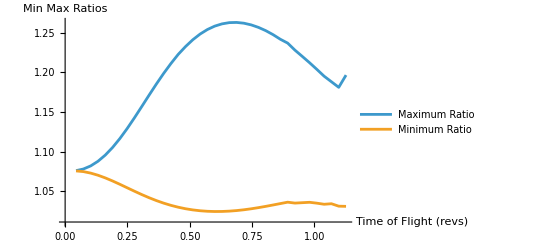

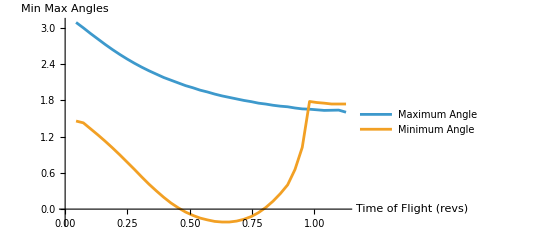

```mathematica
minvals[[;;-3]] // Print
Range[300, 7700, 200] // Print
thetamaxvals[[;;-3]] // Print;

pl= ListLinePlot[ {{Delete[Range[300, 7700, 200], -3]/ (2 Pi / n) ,Delete[maxvals[[;;-3]], -3]} // Transpose, {Delete[Range[300, 7700, 200], -7]/ (2 Pi / n),Delete[minvals[[;;-3]], -7]} // Transpose}, AxesLabel->{"Time of Flight (revs)","Min Max Ratios "}, PlotLegends->{"Maximum Ratio", "Minimum Ratio"} ]
Export["minmaxratiosvstimeenergy2.png",  pl];


pl= ListLinePlot[ {{Delete[Range[300, 7700, 200], -3]/ (2 Pi / n) ,Delete[thetamaxvals[[;; -3]], -3]} // Transpose ,{Range[300, 7700, 200]/ (2 Pi / n) ,thetaminvals[[;; -3]]/. x_Real:>If[x>2.9,x-Pi,x]} // Transpose}, AxesLabel->{"Time of Flight (revs)","Min Max Angles "}, PlotLegends->{"Maximum Angle", "Minimum Angle"} ]
Export["minmaxanglesvstimeenergy2.png",  pl];
```

```mathematica
3000/ (2 Pi / n)
```

0.439279

3414.68

```mathematica
{0,1,2} // Min
```

0